```mathematica
h=73/10; r2=73/10; r1=2;
```

```mathematica
Ω=RegionDifference[Rectangle[{0,0},{r2,h}],Disk[{0,0},2]];
```

```mathematica
<<NDSolve`FEM`
```

```mathematica
Ωmesh=ToElementMesh[Ω,MaxCellMeasure->.001]
```

ElementMesh[{{0.,7.3},{0.,7.3}},{TriangleElement[<79197>]}]

```mathematica
Ωmesh["Wireframe"]
```

-Graphics-

```mathematica
lpc=D[ϕ[r,z],z,z]+D[ϕ[r,z],r,r]+1/r D[ϕ[r,z],r]; TraditionalForm[lpc]
```

ϕ^(0,2)(r,z)+(ϕ^(1,0)(r,z))/r+ϕ^(2,0)(r,z)

```mathematica
solc=NDSolveValue[
{lpc==NeumannValue[0,r==0&&r1<z<h]+NeumannValue[0,z==0&&r1<r<r2],
DirichletCondition[ϕ[r,z]==-1,r^2+z^2==r1^2],
ϕ[r,h]==0,ϕ[r2,z]==0},ϕ,{r,z}∈Ωmesh
]
```

InterpolatingFunction[{{0., 7.3}, {0., 7.3}}, <>]

```mathematica
phiList=Table[Which[r^2+z^2<=r1^2,-1,r>=r2||z>=h,0,True,solc[r,z]],{z,0,730/100,1/100},{r,0,730/100,1/100}];
```

```mathematica
Table[r+.1z,{r,0,10},{z,0,10}]
```

{{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.},{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.},{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.},{3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.},{4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.},{5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.},{6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.},{7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.},{8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.},{9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.},{10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.}}

```mathematica
expFormat[x_]:=Module[{exp,neg},
If[StringLength[x]==0,exp="0",exp=x];
neg=StringTake[exp,1]=="-";
If[neg,exp=StringDrop[exp,1]];
If[StringLength[exp]<2,exp="0"<>exp];
If[neg,"-"<>exp,"+"<>exp]
];
eFormat[x_,m_,n_]:=StringPadLeft[If[x==0,StringPadRight["0.",n+1,"0"]<>"E+00",
NumberForm[SetPrecision[x,n],ScientificNotationThreshold->{0,0},NumberFormat->(Row[{#1, "E", expFormat[#3]}] & )]//ToString],m," "];
```

```mathematica
eFormat[#,12,6]&/@phiList[[1,190;;210]]
```

{-1.00000E+00,-1.00000E+00,-1.00000E+00,-1.00000E+00,-1.00000E+00,-1.00000E+00,-1.00000E+00,-1.00000E+00,-1.00000E+00,-1.00000E+00,-1.00000E+00,-1.00000E+00,-9.93376E-01,-9.86817E-01,-9.80322E-01,-9.73892E-01,-9.67526E-01,-9.61220E-01,-9.54975E-01,-9.48790E-01,-9.42664E-01}

```mathematica
SetDirectory["c:\\git\\ElectronMonteCarlo\\test"]
```

c:\git\ElectronMonteCarlo\test

```mathematica
With[{file=OpenWrite["cwPhi.txt"]},
WriteLine[file,"2/5/2023 Phi from 2D cylindrical solve"];
WriteLine[file,"type cylindrical"];
WriteLine[file,"731 731 .0001 200"];
Do[
WriteLine[file,Row[eFormat[#,14,7]&/@d]],
{d,phiList}
];
Close@file
]
```

cwPhi.txt

```mathematica
SetDirectory["c:\\git\\ElectronMonteCarlo\\test"]
```

c:\git\ElectronMonteCarlo\test

```mathematica
foo=Import["cwPhi.txt","table"];
```

```mathematica
Take[foo,3]
```

{{2/5/2023,Phi,from,2D,cylindrical,solve},{type,cylindrical},{731,731,0.0001,200}}

```mathematica
myPhi=Drop[foo,3];
```

```mathematica
a=100foo[[3,3]]
```

0.01

```mathematica
r1=a foo[[3,4]]
```

2.

```mathematica
r2=a (foo[[3,2]]-1)
```

7.3

```mathematica
h=a (foo[[3,1]]-1)
```

7.3

```mathematica
eField[r_,z_]:=Module[{i,j,α,β,Er,Ez},
If[r^2+z^2<=r1^2||Abs[r]>=r2||Abs[z]>=h,{0,0},
i=Floor[Abs[z]/a]+1;α=Abs[z]/a-(i-1);
j=Floor[r/a]+1;β=r/a-(j-1);
Er=-1/a((1-α)(myPhi[[i,j+1]]-myPhi[[i,j]])+α(myPhi[[i+1,j+1]]-myPhi[[i+1,j]]));
Ez=-Sign[z]/a((1-β)(myPhi[[i+1,j]]-myPhi[[i,j]])+β(myPhi[[i+1,j+1]]-myPhi[[i,j+1]]));
{Er,Ez}
]
]
```

```mathematica
eFieldSol[r_,z_]:=Module[{Er,Ez},
Er=-1/(2a)(solc[r+a,Abs[z]]-solc[r-a,Abs[z]]);
Ez=-1/(2a)(solc[r,Abs[z+a]]-solc[r,Abs[z-a]]);
{Er,Ez}
]
```

```mathematica
eFieldSol2[r_,z_]:=Module[{Er,Ez},
Er=-1/a(solc[r+a/2,Abs[z]]-solc[r-a/2,Abs[z]]);
Ez=-1/a(solc[r,Abs[z+a/2]]-solc[r,Abs[z-a/2]]);
{Er,Ez}
]
```

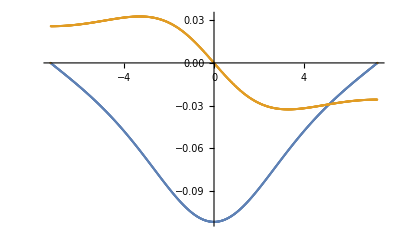

```mathematica
ListPlot[{Table[{z,eField[5,z][[1]]},{z,-7.3,7.3,.01}],Table[{z,eField[5,z][[2]]},{z,-7.3,7.3,.01}]}]
```

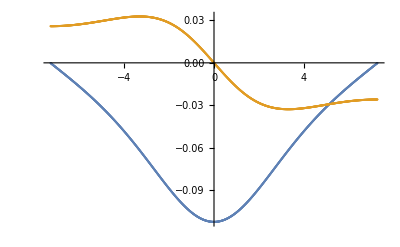

```mathematica
ListPlot[{Table[{z,eFieldSol[5,z][[1]]},{z,-7.29,7.29,.01}],Table[{z,eFieldSol[5,z][[2]]},{z,-7.29,7.29,.01}]}]
```

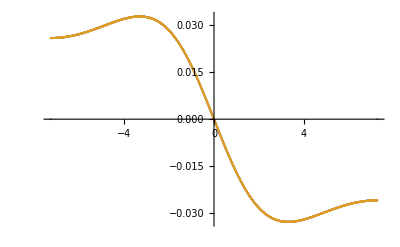

```mathematica
ListPlot[{Table[{z,eField[5,z][[2]]},{z,-7.3,7.3,.01}],Table[{z,eFieldSol[5,z][[2]]},{z,-7.29,7.29,.01}]}]
```

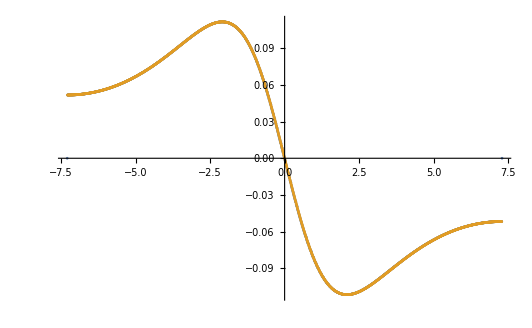

```mathematica
ListPlot[{Table[{z,eField[3,z][[2]]},{z,-7.3,7.3,.01}],Table[{z,eFieldSol[3,z][[2]]},{z,-7.29,7.29,.01}]}]
```

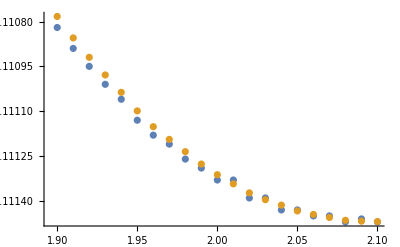

```mathematica
ListPlot[{Table[{z,eField[3,z][[2]]},{z,1.9,2.1,.01}],Table[{z,eFieldSol[3,z][[2]]},{z,1.9,2.1,.01}]}]
```

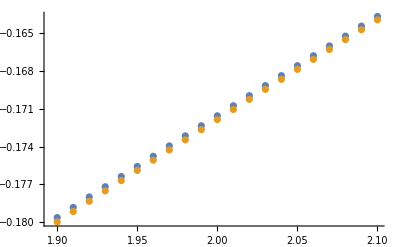

```mathematica
ListPlot[{Table[{z,eField[3,z][[1]]},{z,1.9,2.1,.01}],Table[{z,eFieldSol[3,z][[1]]},{z,1.9,2.1,.01}]}]
```

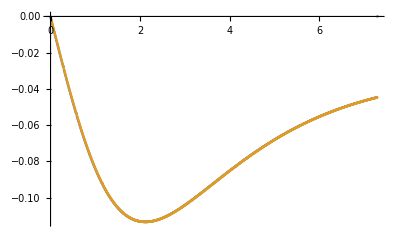

```mathematica
ListPlot[{Table[{r,eField[r,3][[1]]},{r,0,7.3,.01}],Table[{r,eFieldSol[r,3][[1]]},{r,.01,7.29,.01}]}]
```

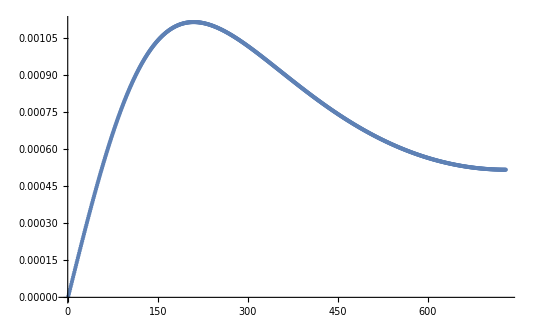

```mathematica
ListPlot[Differences[myPhi[[;;,301]]]]
```

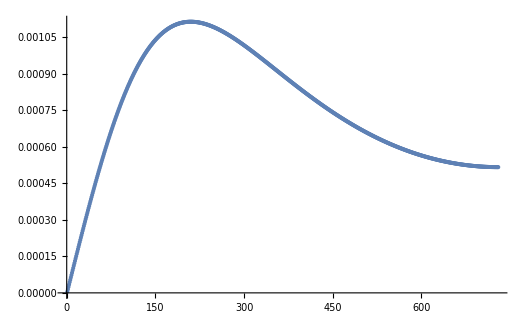

```mathematica
ListPlot[Differences[myPhi[[301,;;]]]]
```

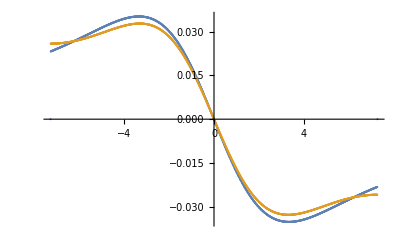

```mathematica
ListPlot[{Table[{z,eField[5,z][[2]]},{z,-7.3,7.3,.01}],Table[{z,eFieldSol2[5,z][[2]]},{z,-7.29,7.29,.01}]}]
```

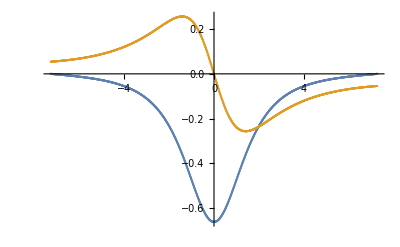

```mathematica
ListPlot[{Table[{z,eField[2,z][[1]]},{z,-7.3,7.3,.01}],Table[{z,eField[2,z][[2]]},{z,-7.3,7.3,.01}]}]
```

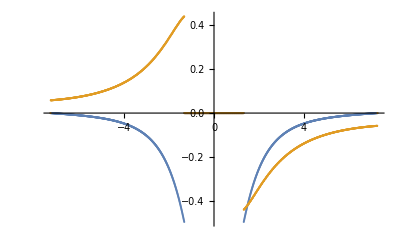

```mathematica
ListPlot[{Table[{z,eField[1.5,z][[1]]},{z,-7.3,7.3,.01}],Table[{z,eField[1.5,z][[2]]},{z,-7.3,7.3,.01}]}]
```

```mathematica
RandomPoint[Ω,20]
```

{{4.60884,6.56359},{3.70718,2.17675},{3.79204,4.78778},{3.85578,6.22376},{0.581694,6.43163},{1.86628,1.5857},{2.90555,0.304272},{4.57528,4.36854},{0.152289,6.79656},{3.08353,1.12602},{0.835754,4.23547},{1.83895,4.89296},{0.692179,1.9846},{1.62829,6.1271},{6.26024,4.0499},{4.3141,6.68255},{3.13939,3.28667},{2.55357,6.45817},{6.46004,2.84543},{5.91566,5.07859}}

```mathematica
testPoints={{4.608842669337616,6.563585696985424},{3.707180200517526,2.176750103748627},{3.792037566239333,4.787781408276944},{3.855778982477084,6.2237642461949205},{0.5816942256367047,6.431626072609152},{1.866278784790517,1.5856972073106224},{2.905554076101517,0.3042719406065806},{4.575278216079155,4.368535882641796},{0.15228864787249807,6.7965613936293},{3.0835338797819465,1.126015266510481},{0.8357538179378818,4.235467354793811},{1.838948320701085,4.892962053921949},{0.6921786231648643,1.984597266088046},{1.6282948913230884,6.1271049030900615},{6.260241423248773,4.049899219509415},{4.314099980656643,6.682551100251801},{3.13939323464767,3.2866671843639033},{2.5535700266727304,6.458169956398989},{6.4600376108498825,2.845434570939234},{5.915655343265746,5.078591103153024}};
```

```mathematica
eField[#[[1]],#[[2]]]&/@testPoints//TableForm
```

-0.00958667 | -0.0314003
-0.125929 | -0.0692497
-0.0390244 | -0.0523992
-0.0145572 | -0.0426574
-0.0031235 | -0.0775592
-0.339956 | -0.287458
-0.313846 | -0.0323101
-0.0442936 | -0.0390171
-0.000472751 | -0.0755912
-0.234641 | -0.083352
-0.0265261 | -0.142051
-0.0306978 | -0.0936121
-0.19912 | -0.569007
-0.010915 | -0.0733952
-0.0388513 | -0.0123728
-0.00811807 | -0.0351415
-0.0881766 | -0.0900567
-0.0101184 | -0.0595603
-0.0527552 | -0.00926054
-0.0269175 | -0.0162529

```mathematica
eFieldSol[#[[1]],#[[2]]]&/@testPoints//TableForm
```

-0.00958476 | -0.0314021
-0.125843 | -0.0692601
-0.0390245 | -0.0523763
-0.0145569 | -0.0426622
-0.00310686 | -0.0775946
-0.339789 | -0.287409
-0.313738 | -0.0322252
-0.0442915 | -0.0390057
-0.000464414 | -0.0755822
-0.234826 | -0.0833969
-0.0265457 | -0.142024
-0.0307354 | -0.0936664
-0.198552 | -0.569194
-0.0109318 | -0.0733708
-0.0388804 | -0.0123714
-0.00811811 | -0.0351454
-0.0881182 | -0.0900225
-0.010116 | -0.0595417
-0.0528019 | -0.00926172
-0.026915 | -0.0162491

```mathematica
comparePoint[rz_,eFunc1_,eFunc2_]:=Module[{e1,e2,n1,n2,diff,cos},
e1=eFunc1[rz[[1]],rz[[2]]];n1=Norm[e1];
e2=eFunc2[rz[[1]],rz[[2]]];n2=Norm[e2];
diff=(2(n1-n2))/(n1+n2);
cos=(e1.e2)/(n1 n2);
{rz,e1,e2,n1,n2,diff,cos}
]
```

```mathematica
comparePoint[testPoints[[1]],eField,eFieldSol]
```

{{4.60884,6.56359},{-0.00958667,-0.0314003},{-0.00958476,-0.0314021},0.0328311,0.0328323,-0.0000366224,1.}

```mathematica
Prepend[comparePoint[#,eField,eFieldSol]&/@testPoints ,{"point","E-FromFile","E-FromLaplace","Norm1","Norm2","diff","cos"}]//TableForm
```

point | E-FromFile | E-FromLaplace | Norm1 | Norm2 | diff | cos
4.60884
6.56359 | -0.00958667
-0.0314003 | -0.00958476
-0.0314021 | 0.0328311 | 0.0328323 | -0.0000366224 | 1.
3.70718
2.17675 | -0.125929
-0.0692497 | -0.125843
-0.0692601 | 0.143714 | 0.143643 | 0.000491844 | 1.
3.79204
4.78778 | -0.0390244
-0.0523992 | -0.0390245
-0.0523763 | 0.0653344 | 0.065316 | 0.000280975 | 1.
3.85578
6.22376 | -0.0145572
-0.0426574 | -0.0145569
-0.0426622 | 0.0450728 | 0.0450773 | -0.0000991408 | 1.
0.581694
6.43163 | -0.0031235
-0.0775592 | -0.00310686
-0.0775946 | 0.0776221 | 0.0776568 | -0.000446556 | 1.
1.86628
1.5857 | -0.339956
-0.287458 | -0.339789
-0.287409 | 0.445199 | 0.44504 | 0.000358306 | 1.
2.90555
0.304272 | -0.313846
-0.0323101 | -0.313738
-0.0322252 | 0.315505 | 0.315389 | 0.000368037 | 1.
4.57528
4.36854 | -0.0442936
-0.0390171 | -0.0442915
-0.0390057 | 0.0590275 | 0.0590185 | 0.000152736 | 1.
0.152289
6.79656 | -0.000472751
-0.0755912 | -0.000464414
-0.0755822 | 0.0755926 | 0.0755836 | 0.000119727 | 1.
3.08353
1.12602 | -0.234641
-0.083352 | -0.234826
-0.0833969 | 0.249006 | 0.249195 | -0.000759704 | 1.
0.835754
4.23547 | -0.0265261
-0.142051 | -0.0265457
-0.142024 | 0.144506 | 0.144484 | 0.000153244 | 1.
1.83895
4.89296 | -0.0306978
-0.0936121 | -0.0307354
-0.0936664 | 0.0985169 | 0.0985802 | -0.000642098 | 1.
0.692179
1.9846 | -0.19912
-0.569007 | -0.198552
-0.569194 | 0.602842 | 0.60283 | 0.0000188315 | 1.
1.62829
6.1271 | -0.010915
-0.0733952 | -0.0109318
-0.0733708 | 0.0742024 | 0.0741807 | 0.000292952 | 1.
6.26024
4.0499 | -0.0388513
-0.0123728 | -0.0388804
-0.0123714 | 0.0407739 | 0.0408012 | -0.000668778 | 1.
4.3141
6.68255 | -0.00811807
-0.0351415 | -0.00811811
-0.0351454 | 0.036067 | 0.0360708 | -0.000107433 | 1.
3.13939
3.28667 | -0.0881766
-0.0900567 | -0.0881182
-0.0900225 | 0.126037 | 0.125972 | 0.000518181 | 1.
2.55357
6.45817 | -0.0101184
-0.0595603 | -0.010116
-0.0595417 | 0.0604137 | 0.0603949 | 0.000310476 | 1.
6.46004
2.84543 | -0.0527552
-0.00926054 | -0.0528019
-0.00926172 | 0.0535619 | 0.053608 | -0.000860853 | 1.
5.91566
5.07859 | -0.0269175
-0.0162529 | -0.026915
-0.0162491 | 0.0314437 | 0.0314397 | 0.000128765 | 1.

```mathematica
Grid[Prepend[comparePoint[#,eField,eFieldSol]&/@testPoints ,{"point","E-FromFile","E-FromLaplace","Norm1","Norm2","diff","cos"}],Frame->All,Spacings->2]
```

point | E-FromFile | E-FromLaplace | Norm1 | Norm2 | diff | cos
{4.60884,6.56359} | {-0.00958667,-0.0314003} | {-0.00958476,-0.0314021} | 0.0328311 | 0.0328323 | -0.0000366224 | 1.
{3.70718,2.17675} | {-0.125929,-0.0692497} | {-0.125843,-0.0692601} | 0.143714 | 0.143643 | 0.000491844 | 1.
{3.79204,4.78778} | {-0.0390244,-0.0523992} | {-0.0390245,-0.0523763} | 0.0653344 | 0.065316 | 0.000280975 | 1.
{3.85578,6.22376} | {-0.0145572,-0.0426574} | {-0.0145569,-0.0426622} | 0.0450728 | 0.0450773 | -0.0000991408 | 1.
{0.581694,6.43163} | {-0.0031235,-0.0775592} | {-0.00310686,-0.0775946} | 0.0776221 | 0.0776568 | -0.000446556 | 1.
{1.86628,1.5857} | {-0.339956,-0.287458} | {-0.339789,-0.287409} | 0.445199 | 0.44504 | 0.000358306 | 1.
{2.90555,0.304272} | {-0.313846,-0.0323101} | {-0.313738,-0.0322252} | 0.315505 | 0.315389 | 0.000368037 | 1.
{4.57528,4.36854} | {-0.0442936,-0.0390171} | {-0.0442915,-0.0390057} | 0.0590275 | 0.0590185 | 0.000152736 | 1.
{0.152289,6.79656} | {-0.000472751,-0.0755912} | {-0.000464414,-0.0755822} | 0.0755926 | 0.0755836 | 0.000119727 | 1.
{3.08353,1.12602} | {-0.234641,-0.083352} | {-0.234826,-0.0833969} | 0.249006 | 0.249195 | -0.000759704 | 1.
{0.835754,4.23547} | {-0.0265261,-0.142051} | {-0.0265457,-0.142024} | 0.144506 | 0.144484 | 0.000153244 | 1.
{1.83895,4.89296} | {-0.0306978,-0.0936121} | {-0.0307354,-0.0936664} | 0.0985169 | 0.0985802 | -0.000642098 | 1.
{0.692179,1.9846} | {-0.19912,-0.569007} | {-0.198552,-0.569194} | 0.602842 | 0.60283 | 0.0000188315 | 1.
{1.62829,6.1271} | {-0.010915,-0.0733952} | {-0.0109318,-0.0733708} | 0.0742024 | 0.0741807 | 0.000292952 | 1.
{6.26024,4.0499} | {-0.0388513,-0.0123728} | {-0.0388804,-0.0123714} | 0.0407739 | 0.0408012 | -0.000668778 | 1.
{4.3141,6.68255} | {-0.00811807,-0.0351415} | {-0.00811811,-0.0351454} | 0.036067 | 0.0360708 | -0.000107433 | 1.
{3.13939,3.28667} | {-0.0881766,-0.0900567} | {-0.0881182,-0.0900225} | 0.126037 | 0.125972 | 0.000518181 | 1.
{2.55357,6.45817} | {-0.0101184,-0.0595603} | {-0.010116,-0.0595417} | 0.0604137 | 0.0603949 | 0.000310476 | 1.
{6.46004,2.84543} | {-0.0527552,-0.00926054} | {-0.0528019,-0.00926172} | 0.0535619 | 0.053608 | -0.000860853 | 1.
{5.91566,5.07859} | {-0.0269175,-0.0162529} | {-0.026915,-0.0162491} | 0.0314437 | 0.0314397 | 0.000128765 | 1.

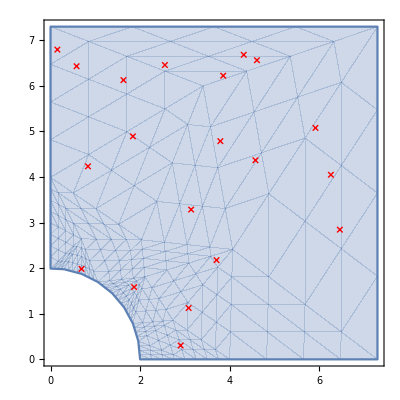

```mathematica
Show[RegionPlot[Ω],ListPlot[testPoints,PlotMarkers->Style["×",Red,Large]]]
```

```mathematica
TableForm@testPoints
```

4.60884 | 6.56359
3.70718 | 2.17675
3.79204 | 4.78778
3.85578 | 6.22376
0.581694 | 6.43163
1.86628 | 1.5857
2.90555 | 0.304272
4.57528 | 4.36854
0.152289 | 6.79656
3.08353 | 1.12602
0.835754 | 4.23547
1.83895 | 4.89296
0.692179 | 1.9846
1.62829 | 6.1271
6.26024 | 4.0499
4.3141 | 6.68255
3.13939 | 3.28667
2.55357 | 6.45817
6.46004 | 2.84543
5.91566 | 5.07859

```mathematica
nearbyFieldNorm=Table[{theta,Norm[eField[(r1+a)Cos[theta],(r1+a)Sin[theta]]]},{theta,0,π/2,1/100 π/2}];
```

```mathematica
nearbyFieldNormSol=Table[{theta,Norm[eFieldSol[(r1+a)Cos[theta],(r1+a)Sin[theta]]]},{theta,π/200,π/2,1/100 π/2}];
```

InterpolatingFunction::femdmval: Input value {-0.01,2.01} lies outside the range of data in the interpolating function.

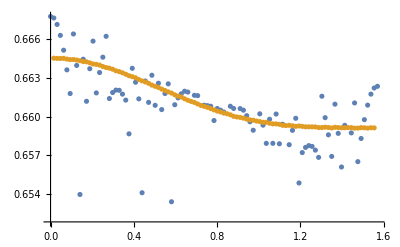

```mathematica
ListPlot[{nearbyFieldNorm,nearbyFieldNormSol}]
```

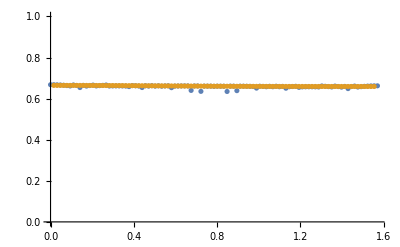

```mathematica
ListPlot[{nearbyFieldNorm,nearbyFieldNormSol},PlotRange->{All,{0,1}}]
```

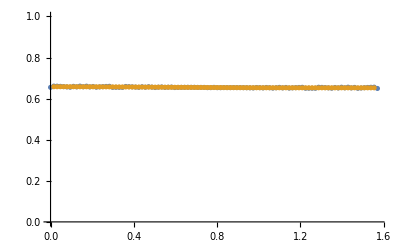

```mathematica
ListPlot[{nearbyFieldNorm2,nearbyFieldNormSol2},PlotRange->{All,{0,1}}]
```

```mathematica
nearbyFieldNorm2=Table[{theta,Norm[eField[(r1+2a)Cos[theta],(r1+2a)Sin[theta]]]},{theta,0,π/2,1/100 π/2}];
```

```mathematica
nearbyFieldNormSol2=Table[{theta,Norm[eFieldSol[(r1+2a)Cos[theta],(r1+2a)Sin[theta]]]},{theta,π/200,π/2,1/100 π/2}];
```

InterpolatingFunction::femdmval: Input value {-0.01,2.02} lies outside the range of data in the interpolating function.

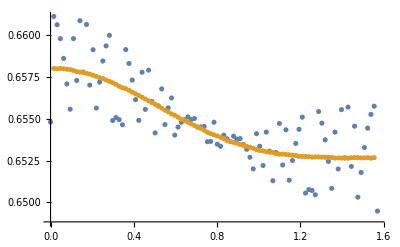

```mathematica
ListPlot[{nearbyFieldNorm2,nearbyFieldNormSol2}]
```

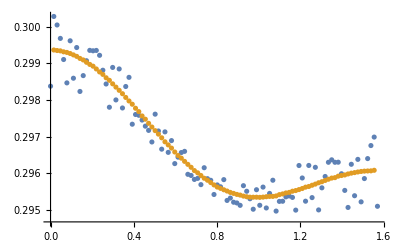

```mathematica
With[{n=100},
ListPlot[{Table[{theta,Norm[eField[(r1+n a)Cos[theta],(r1+n a)Sin[theta]]]},{theta,0,π/2,1/100 π/2}],
Table[{theta,Norm[eFieldSol[(r1+n a)Cos[theta],(r1+n a)Sin[theta]]]},{theta,π/200,π/2-π/200,1/100 π/2}]}]
]
```

```mathematica
nearbyFieldCos=Table[ee=eField[(r1+a)Cos[theta],(r1+a)Sin[theta]];{theta,ee.{Cos[theta],Sin[theta]}/Norm[ee]},{theta,0,π/2,1/100 π/2}];
```

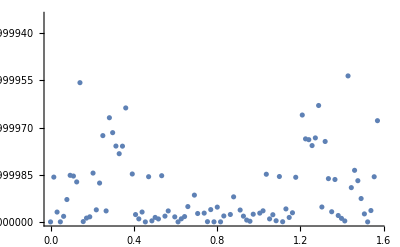

```mathematica
ListPlot[nearbyFieldCos]
```

```mathematica
ArcCos[.999995] 180/π
```

0.181185